## Initialization

### Import dependencies

```mathematica
(* Run bubble-4a-murphree.nb before. *)
```

```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"}
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"}
```

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

```mathematica
If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]
```

```mathematica
Get["MovingTrap-murphree.m"]
Get["FitCurveHacked-mean-murphree.m"]
Get["SMThreeTraps.m"]
Get["SMThreeChipModel.m"]
```

Syntax::sntx: Invalid syntax in or before 
    "{{eVec1,\!\(\*SubscriptBox[\(ω\),
        \(1\)]\)},{eVec2,\!\(\*SubscriptBox[\(ω\),
        \(2\)]\)},{eVec3,\!\(\*SubscriptBox[\(ω\), \(3\)]\)}}."*);
                                                                                        
                                                                                ^
      " (line 73 of "MovingTrap-murphree.m").

The following variables used by ExpansionPlotHacked are protected by this package: {axis, trap, usemodel, frequency, trapposition, gridlines, size, meanfrequency, meanmodel}

### Define initial and final trap parameters

```mathematica
trapzero=convertCALTableToTrapParameters@tableZLHb
trapone=convertCALTableToTrapParameters@tableZHbB3
```

{0.,0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0.,0,0.,2.425,2.6,-1.95,3.55435,-3.11335}

### Define target ramp analytic function

```mathematica
(*cass[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2 t^(1/4) -1)]/Tanh[5];
cassShort[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2(t/2)^(1/4) -1)]/Tanh[5];*)
```

```mathematica
(*omegaPlot=Plot[cassShort[800,50,t]^2,{t,0,1},PlotRange->All];
dOmegaPlot=Plot[Evaluate[(1/0.5)*Abs@D[cassShort[800,50,t],t]],{t,0,1},PlotRange->All,PlotStyle->{"Red"}];
Show[omegaPlot,dOmegaPlot,PlotRange->{{0,1},{0,6400}}]*)
```

```mathematica
(*periodT=0.250 (* [s] *);
omegaI=800 (* [Hz] *);
omegaF=20 (* [Hz] *);
Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->All,PlotStyle->{"Blue","Red"}]*)
```

```mathematica
(*Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->{{0,1},{0,1*10^4}},PlotStyle->{"Blue","Red"}]*)
```

```mathematica
(*
*)
```

```mathematica
(*num=20;
times={0,0.0085,0.017,0.024,0.032,0.04,0.047,0.056,0.068,0.095,0.127,0.142,0.157,0.172,0.189,0.208,0.233,0.267,0.33,0.4,1};
Length@times
Plot[Evaluate[D[cassShort[1,0,t],{t,1}]],{t,0,1},GridLines->{times,Table[-k*max/(num/2),{k,1,num/2}]}]*)
```

```mathematica
(*Length@Differences@times*)
```

```mathematica
(*Plot[cassShort[1,0,t],{t,0,1},GridLines->{times,{}},PlotRange->Full]*)
```

```mathematica
(*max=MaxValue[{Abs@Evaluate[D[cassShort[1,0,t],{t,1}]],t>0.01},t]*)
```

```mathematica
(*dCassShort[t_]=Evaluate[D[cassShort[1,0,t],{t,1}]];*)
```

```mathematica
(*(*InverseFunction@dCassShort*)*)
```

```mathematica
(*(*cassShortInv=InverseFunction@dCassShort*)*)
```

```mathematica
(*(*cassShortInv[-max]*)*)
```

```mathematica
(*Plot[Evaluate[D[cassShort[1,0,t],{t,2}]],{t,0,1},PlotRange->{{0,1},{-80,40}}]*)
```

```mathematica
(*corgierSimp[t_]:=Module[{tau=2*Pi*t},
(1/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];*)
```

```mathematica
(*Plot[1-corgierSimp[t],{t,0,1}]*)
```

```mathematica
(*Plot[Evaluate@D[1-corgierSimp[t],t],{t,0,1}]*)
```

```mathematica
(*InverseFunction[corgierSimp][8/3]*)
```

```mathematica
(*Plot[Evaluate@D[1-corgierSimp[t],{t,2}],{t,0,1}]*)
```

```mathematica
(*ArcCos[-1-2*Sqrt[2*6/10]]/(2*Pi)//N*)
```

```mathematica
(*trapAnalytic[trap1_,trap2_,t_]:=trap1+(trap2-trap1)*(1-cassShort[1,0,t]);
zeroCrossing[trap1_,trap2_]:=(1/8)*((1/5)*ArcTanh[2*Tanh[5]*((1/2)-trap2[[6]]/(trap2[[6]]-trap1[[6]]))]+1)^4;*)
```

```mathematica
(*Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All]
tauZero=zeroCrossing[trapzero,trapone]
period=500*10^(-3);
deltaTau=10*^-3/period;
newTaus={tauZero-deltaTau,tauZero,tauZero+deltaTau};
Print["tZero = "<>ToString[tauZero*period]]*)
```

```mathematica
(*Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,rampin1sguess⟦1⟧}]*)
```

```mathematica
(*Show[{
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All],
ListPlot[Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,Accumulate@rampin1sguess⟦1⟧}]]
}]*)
```

### Define ramp ansatz

#### Trap 1 Short

The first component of this object defines how to distribute the duration of each linear ramp in the ramp sequence. The durations are expressed as a fraction of the ramp sequence’s total duration, and so must sum to 1.

The second component of this object nominally is a guess at the fractional change of the ramp sequence for that linear ramp, but is not used by any of the fitting components and is considered vestigial.

```mathematica
rampin1sguess={2*{0.01,0.01,0.01,0.01,0.01,0.01,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.025,0.04,0.07,0.08,0.09},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

Check that both components sum to 1.

```mathematica
Total[rampin1sguess⟦1⟧]
Total[rampin1sguess⟦2⟧]
```

1.

1.

Check the specified number of constituent linear ramps.

```mathematica
numberOfSequencePoints=Length@rampin1sguess⟦1⟧
```

20

## Calculate ramp

The following took 40 minutes to complete. (29 Sept. 2020)

```mathematica
(* 
If FitCurveHacked runs in less than a second and has multiple errors citing GeometricMean, go back and make sure bubble-4a.nb was run before this notebook. MovingTrap-murphree.m calls ChipTrapFrequencies, which is defined in that notebook.
*)
```

```mathematica
(rampin1s=FitCurveHacked[trapzero,trapone,rampin1sguess,numberOfSequencePoints,-3.5,-5])//Timing
```

{0.01982,0.215963,0.146368,462.856,463.072,1.,0}

{0.50991,-267.452,0.146368,462.856,195.404,1.,0.01982}

{0.26486,-136.303,0.146368,462.856,326.553,0.50991,0.01982}

{0.14234,-67.8018,0.146368,462.856,395.054,0.26486,0.01982}

{0.08108,-33.6483,0.146368,462.856,429.208,0.14234,0.01982}

{0.05045,-16.6712,0.146368,462.856,446.185,0.08108,0.01982}

{0.03513,-8.21264,0.146368,462.856,454.644,0.05045,0.01982}

{0.02747,-3.99241,0.146368,462.856,458.864,0.03513,0.01982}

{0.02364,-1.88467,0.146368,462.856,460.972,0.02747,0.01982}

{0.02173,-0.834149,0.146368,462.856,462.022,0.02364,0.01982}

{0.02078,-0.311791,0.146368,462.856,462.544,0.02173,0.01982}

Completed point 1 of 19 in 69.6875 s (Total time: 1.16146 min).

{0.0407547,1.12586,0.138884,439.191,440.317,0.9797,0}

{0.51023,-253.99,0.138884,439.191,185.201,0.9797,0.0407547}

{0.27549,-129.821,0.138884,439.191,309.37,0.51023,0.0407547}

{0.15812,-64.3234,0.138884,439.191,374.867,0.27549,0.0407547}

{0.09944,-31.5122,0.138884,439.191,407.679,0.15812,0.0407547}

{0.0701,-15.1638,0.138884,439.191,424.027,0.09944,0.0407547}

{0.05543,-7.0117,0.138884,439.191,432.179,0.0701,0.0407547}

{0.04809,-2.93931,0.138884,439.191,436.251,0.05543,0.0407547}

{0.04442,-0.904823,0.138884,439.191,438.286,0.04809,0.0407547}

Completed point 2 of 19 in 58.2344 s (Total time: 2.13203 min).

{0.0634428,0.864588,0.127482,403.134,403.998,0.93711,0}

{0.50028,-233.677,0.127482,403.134,169.457,0.93711,0.0634428}

{0.28186,-120.732,0.127482,403.134,282.401,0.50028,0.0634428}

{0.17265,-60.2244,0.127482,403.134,342.909,0.28186,0.0634428}

{0.11805,-29.677,0.127482,403.134,373.457,0.17265,0.0634428}

{0.09075,-14.3985,0.127482,403.134,388.735,0.11805,0.0634428}

{0.0771,-6.76554,0.127482,403.134,396.368,0.09075,0.0634428}

{0.07027,-2.94872,0.127482,403.134,400.185,0.0771,0.0634428}

{0.06686,-1.04382,0.127482,403.134,402.09,0.07027,0.0634428}

Completed point 3 of 19 in 58.3906 s (Total time: 3.10521 min).

{0.0824224,-0.999855,0.113188,357.932,356.932,0.87196,0}

{0.04121,22.0687,0.113188,357.932,380.,0.0824224,0}

{0.06182,10.5314,0.113188,357.932,368.463,0.0824224,0.04121}

{0.07212,4.76576,0.113188,357.932,362.697,0.0824224,0.06182}

{0.07727,1.88338,0.113188,357.932,359.815,0.0824224,0.07212}

{0.07985,0.439555,0.113188,357.932,358.371,0.0824224,0.07727}

{0.08114,-0.282307,0.113188,357.932,357.649,0.0824224,0.07985}

Completed point 4 of 19 in 46.3281 s (Total time: 3.87734 min).

{0.0925325,-2.28195,0.0976281,308.727,306.445,0.79146,0}

{0.04627,23.4262,0.0976281,308.727,332.153,0.0925325,0}

{0.0694,10.5486,0.0976281,308.727,319.276,0.0925325,0.04627}

{0.08097,4.12431,0.0976281,308.727,312.851,0.0925325,0.0694}

{0.08675,0.920039,0.0976281,308.727,309.647,0.0925325,0.08097}

{0.08964,-0.680735,0.0976281,308.727,308.046,0.0925325,0.08675}

{0.0882,0.116766,0.0976281,308.727,308.844,0.08964,0.08675}

{0.08892,-0.282014,0.0976281,308.727,308.445,0.08964,0.0882}

Completed point 5 of 19 in 54.2344 s (Total time: 4.78125 min).

{0.0952173,-4.01586,0.0824107,260.605,256.59,0.7029,0}

{0.04761,21.8178,0.0824107,260.605,282.423,0.0952173,0}

{0.07141,8.84595,0.0824107,260.605,269.451,0.0952173,0.04761}

{0.08331,2.40162,0.0824107,260.605,263.007,0.0952173,0.07141}

{0.08926,-0.809146,0.0824107,260.605,259.796,0.0952173,0.08331}

{0.08628,0.797954,0.0824107,260.605,261.403,0.08926,0.08331}

Completed point 6 of 19 in 39.75 s (Total time: 5.44375 min).

{0.133299,-6.43093,0.0625263,197.726,191.295,0.61513,0}

{0.06665,27.4985,0.0625263,197.726,225.224,0.133299,0}

{0.09997,10.3251,0.0625263,197.726,208.051,0.133299,0.06665}

{0.11663,1.89264,0.0625263,197.726,199.618,0.133299,0.09997}

{0.12496,-2.28154,0.0625263,197.726,195.444,0.133299,0.11663}

{0.1208,-0.200563,0.0625263,197.726,197.525,0.12496,0.11663}

{0.11872,0.842635,0.0625263,197.726,198.568,0.1208,0.11663}

{0.11976,0.320812,0.0625263,197.726,198.046,0.1208,0.11872}

Completed point 7 of 19 in 54.8125 s (Total time: 6.35729 min).

{0.112691,-5.04517,0.0472466,149.407,144.362,0.49485,0}

{0.05635,20.8425,0.0472466,149.407,170.249,0.112691,0}

{0.08452,7.6729,0.0472466,149.407,157.08,0.112691,0.05635}

{0.09861,1.2528,0.0472466,149.407,150.66,0.112691,0.08452}

{0.10565,-1.91105,0.0472466,149.407,147.496,0.112691,0.09861}

{0.10213,-0.332848,0.0472466,149.407,149.074,0.10565,0.09861}

{0.10037,0.45905,0.0472466,149.407,149.866,0.10213,0.09861}

{0.10125,0.0628687,0.0472466,149.407,149.47,0.10213,0.10037}

{0.10169,-0.135048,0.0472466,149.407,149.272,0.10213,0.10125}

Completed point 8 of 19 in 60.4063 s (Total time: 7.36406 min).

{0.0902858,-3.0598,0.036193,114.452,111.393,0.39338,0}

{0.04514,15.2501,0.036193,114.452,129.703,0.0902858,0}

{0.06771,5.91916,0.036193,114.452,120.372,0.0902858,0.04514}

{0.079,1.38387,0.036193,114.452,115.836,0.0902858,0.06771}

{0.08464,-0.848131,0.036193,114.452,113.604,0.0902858,0.079}

{0.08182,0.26505,0.036193,114.452,114.717,0.08464,0.079}

{0.08323,-0.292246,0.036193,114.452,114.16,0.08464,0.08182}

Completed point 9 of 19 in 46.9063 s (Total time: 8.14583 min).

{0.0696418,-1.13901,0.0283956,89.7947,88.6557,0.31086,0}

{0.03482,11.3171,0.0283956,89.7947,101.112,0.0696418,0}

{0.05223,4.98038,0.0283956,89.7947,94.7751,0.0696418,0.03482}

{0.06094,1.89212,0.0283956,89.7947,91.6868,0.0696418,0.05223}

{0.06529,0.37012,0.0283956,89.7947,90.1648,0.0696418,0.06094}

{0.06747,-0.387547,0.0283956,89.7947,89.4072,0.0696418,0.06529}

Completed point 10 of 19 in 39.5625 s (Total time: 8.80521 min).

{0.054088,-0.478708,0.022922,72.4858,72.0071,0.24448,0}

{0.02704,8.16006,0.022922,72.4858,80.6459,0.054088,0}

{0.04056,3.78038,0.022922,72.4858,76.2662,0.054088,0.02704}

{0.04732,1.63689,0.022922,72.4858,74.1227,0.054088,0.04056}

{0.0507,0.576563,0.022922,72.4858,73.0624,0.054088,0.04732}

{0.05239,0.0492294,0.022922,72.4858,72.535,0.054088,0.0507}

{0.05324,-0.215287,0.022922,72.4858,72.2705,0.054088,0.05239}

{0.05282,-0.0846441,0.022922,72.4858,72.4012,0.05324,0.05239}

Completed point 11 of 19 in 52.5781 s (Total time: 9.68151 min).

{0.0414533,-0.152147,0.019057,60.2637,60.1115,0.19188,0}

{0.02073,5.89112,0.019057,60.2637,66.1548,0.0414533,0}

{0.03109,2.8371,0.019057,60.2637,63.1008,0.0414533,0.02073}

{0.03627,1.33483,0.019057,60.2637,61.5985,0.0414533,0.03109}

{0.03886,0.589802,0.019057,60.2637,60.8535,0.0414533,0.03627}

{0.04016,0.217369,0.019057,60.2637,60.481,0.0414533,0.03886}

{0.04081,0.0315336,0.019057,60.2637,60.2952,0.0414533,0.04016}

{0.04113,-0.0598619,0.019057,60.2637,60.2038,0.0414533,0.04081}

Completed point 12 of 19 in 53.9063 s (Total time: 10.5799 min).

{0.0317238,-0.0526055,0.0162972,51.5361,51.4835,0.15091,0}

{0.01586,4.25799,0.0162972,51.5361,55.7941,0.0317238,0}

{0.02379,2.08522,0.0162972,51.5361,53.6213,0.0317238,0.01586}

{0.02776,1.01099,0.0162972,51.5361,52.5471,0.0317238,0.02379}

{0.02974,0.478581,0.0162972,51.5361,52.0147,0.0317238,0.02776}

{0.03073,0.213211,0.0162972,51.5361,51.7493,0.0317238,0.02974}

{0.03123,0.079397,0.0162972,51.5361,51.6155,0.0317238,0.03073}

Completed point 13 of 19 in 46.4844 s (Total time: 11.3547 min).

{0.0247786,-0.121812,0.0142997,45.2195,45.0977,0.11943,0}

{0.01239,3.06014,0.0142997,45.2195,48.2796,0.0247786,0}

{0.01858,1.45939,0.0142997,45.2195,46.6789,0.0247786,0.01239}

{0.02168,0.66587,0.0142997,45.2195,45.8853,0.0247786,0.01858}

{0.02323,0.271163,0.0142997,45.2195,45.4906,0.0247786,0.02168}

{0.024,0.0755913,0.0142997,45.2195,45.2951,0.0247786,0.02323}

{0.02439,-0.023335,0.0142997,45.2195,45.1961,0.0247786,0.024}

{0.0242,0.024849,0.0142997,45.2195,45.2443,0.02439,0.024}

Completed point 14 of 19 in 53.5938 s (Total time: 12.2479 min).

{0.0194383,-0.183253,0.0128334,40.5828,40.3996,0.09513,0}

{0.00972,2.19839,0.0128334,40.5828,42.7812,0.0194383,0}

{0.01458,1.00027,0.0128334,40.5828,41.5831,0.0194383,0.00972}

{0.01701,0.406508,0.0128334,40.5828,40.9893,0.0194383,0.01458}

{0.01822,0.112188,0.0128334,40.5828,40.695,0.0194383,0.01701}

{0.01883,-0.0358488,0.0128334,40.5828,40.547,0.0194383,0.01822}

{0.01852,0.0393543,0.0128334,40.5828,40.6222,0.01883,0.01822}

Completed point 15 of 19 in 46.0938 s (Total time: 13.0161 min).

{0.02254,-0.0378248,0.0111687,35.3184,35.2806,0.07645,0}

{0.01127,2.57101,0.0111687,35.3184,37.8894,0.02254,0}

{0.0169,1.25654,0.0111687,35.3184,36.575,0.02254,0.01127}

{0.01972,0.606466,0.0111687,35.3184,35.9249,0.02254,0.0169}

{0.02113,0.283585,0.0111687,35.3184,35.602,0.02254,0.01972}

{0.02184,0.121555,0.0111687,35.3184,35.44,0.02254,0.02113}

{0.02219,0.0418194,0.0111687,35.3184,35.3602,0.02254,0.02184}

Completed point 16 of 19 in 45.6875 s (Total time: 13.7776 min).

{0.021035,0.145356,0.00966805,30.5731,30.7184,0.05409,0}

{0.03756,-3.15265,0.00966805,30.5731,27.4204,0.05409,0.021035}

{0.0293,-1.54544,0.00966805,30.5731,29.0276,0.03756,0.021035}

{0.02517,-0.710138,0.00966805,30.5731,29.8629,0.0293,0.021035}

{0.0231,-0.284182,0.00966805,30.5731,30.2889,0.02517,0.021035}

{0.02207,-0.0704976,0.00966805,30.5731,30.5026,0.0231,0.021035}

{0.02155,0.0378101,0.00966805,30.5731,30.6109,0.02207,0.021035}

{0.02181,-0.0163794,0.00966805,30.5731,30.5567,0.02207,0.02155}

{0.02168,0.0107065,0.00966805,30.5731,30.5838,0.02181,0.02155}

Completed point 17 of 19 in 57.0156 s (Total time: 14.7279 min).

{0.01694,0.195108,0.00854269,27.0144,27.2095,0.03235,0}

{0.02464,-1.20865,0.00854269,27.0144,25.8057,0.03235,0.01694}

{0.02079,-0.516832,0.00854269,27.0144,26.4975,0.02464,0.01694}

{0.01886,-0.162502,0.00854269,27.0144,26.8519,0.02079,0.01694}

{0.0179,0.0156655,0.00854269,27.0144,27.03,0.01886,0.01694}

{0.01838,-0.0735777,0.00854269,27.0144,26.9408,0.01886,0.0179}

{0.01814,-0.028996,0.00854269,27.0144,26.9854,0.01838,0.0179}

Completed point 18 of 19 in 45.6406 s (Total time: 15.4885 min).

{0.00862,-0.0980719,0.00808013,25.5516,25.4535,0.01433,0}

{0.00431,0.666829,0.00808013,25.5516,26.2184,0.00862,0}

{0.00646,0.282451,0.00808013,25.5516,25.8341,0.00862,0.00431}

{0.00754,0.0915324,0.00808013,25.5516,25.6432,0.00862,0.00646}

Completed point 19 of 19 in 27.5 s (Total time: 15.9469 min).

{959.859,{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.0203,0.04259,0.06515,0.0805,0.08856,0.08777,0.12028,0.10147,0.08252,0.06638,0.0526,0.04097,0.03148,0.0243,0.01868,0.02236,0.02174,0.01802,0.00808,0.00625}}}

```mathematica
(*corgierSin[t_,ωi_,ωf_]:=Module[{tau=2*Pi*t},
ωi+((ωf-ωi)/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];*)
```

```mathematica
(*Plot[corgierSin[t,1,0],{t,0,1}]*)
```

```mathematica
(*omegaMeanVF[trap0_,trap1_,fColl0_:0,fColl1_:1,deltaFColl_:0.1]:=Module[
{trapParametersVF=Table[trap0+(trap1-trap0)*fColl,{fColl,fColl0,fColl1,deltaFColl}],
omegasVF,omegaMeanVF},
omegasVF=Map[ChipTrapABFrequencies@@#&,trapParametersVF];
Return[Map[GeometricMean[#[[4]]]&,omegasVF]];
];*)
```

```mathematica
Beep[];
```

The following took ~8 1/2 minutes to run.

```mathematica
points1s=100;
(pts1s=MovingTrap[trapzero,trapone,rampin1s,points1s,numberOfSequencePoints];)//Timing
```

{287.,Null}

```mathematica
Length@pts1s
```

101

### Plot calculated ramp’s parameters

{{0.,1.},{0.668033,6.83526}}

{1.9504,930.072}

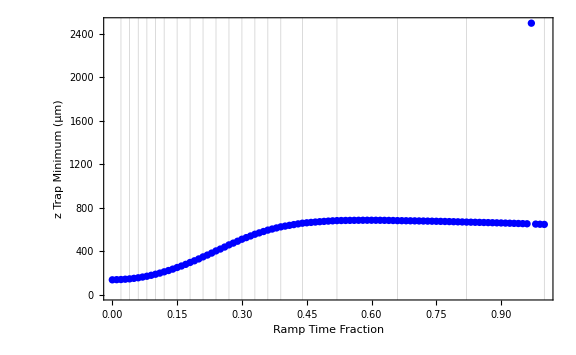
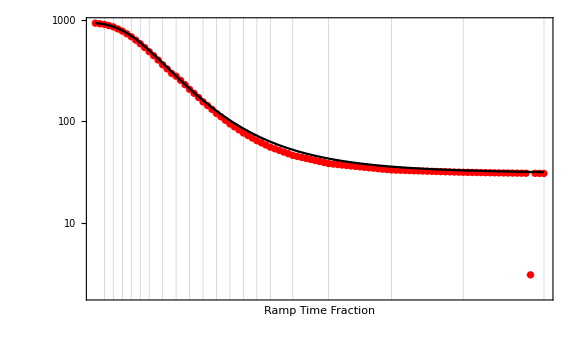

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"z"]
```

{{0.,1.},{1.8051,4.77184}}

{6.08059,118.137}

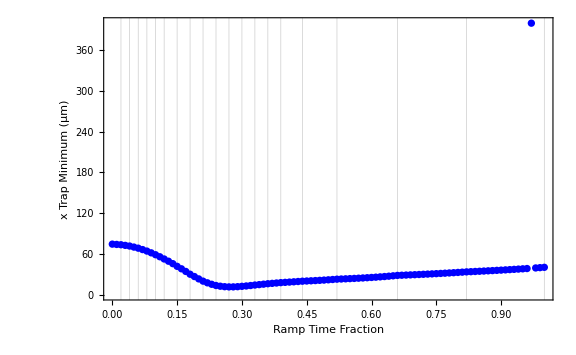
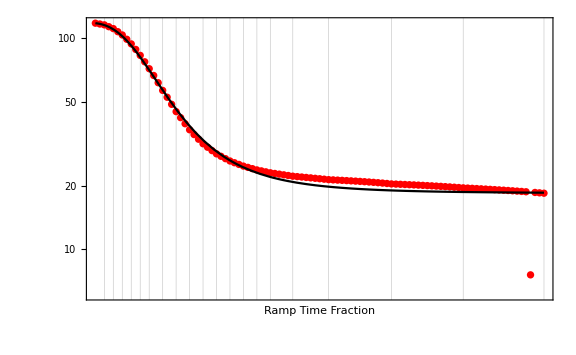

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"x",meanfrequency->False]
```

{{0.,1.},{0.965391,6.87617}}

{2.62581,968.904}

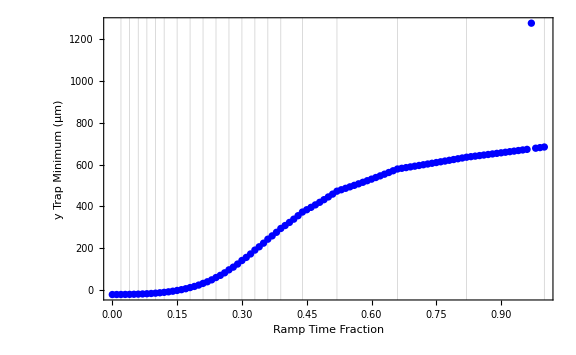
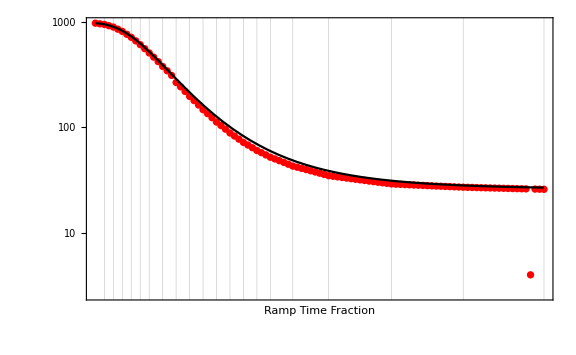

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"y",meanfrequency->False]
```

{{0.,1.},{0.668033,6.83526}}

{1.9504,930.072}

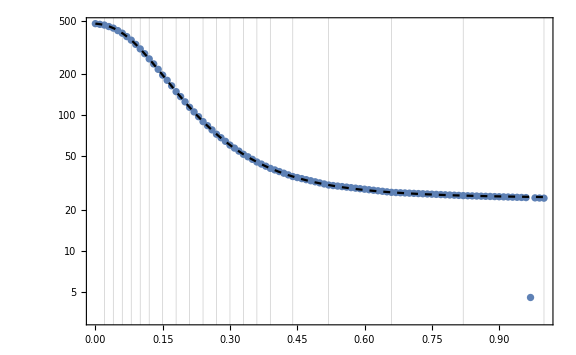

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->False,frequency->False,gridlines->True,usemodel->True,size->Large,axis->"z",meanfrequency->True,meanmodel->True]
```

```mathematica
Beep[]
```

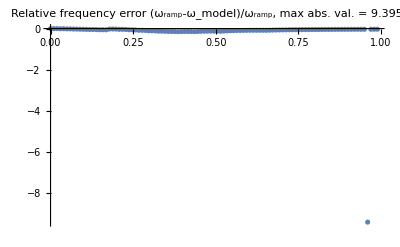

```mathematica
plotFreqError[pts1s]
```

## Export ramp

### Export ramp

```mathematica
trap1short={#⟦1⟧,Table[Total[Take[Round[#⟦2⟧,10.^-5],n]],{n,Length@rampin1s⟦1⟧}]}&[rampin1s]
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.0203,0.06289,0.12804,0.20854,0.2971,0.38487,0.50515,0.60662,0.68914,0.75552,0.80812,0.84909,0.88057,0.90487,0.92355,0.94591,0.96765,0.98567,0.99375,1.}}

```mathematica
(* Set the DateStringFormat to help create unique names for each exported beam.The format is inspired by the ISO 8601 standard. *)
generateTimeStamp[]:=DateString[{"Year","Month","Day","T","Hour","Minute","Second"}];
rampTimeStamp=generateTimeStamp[]
```

20201111T171033

```mathematica
Export[FileNameJoin@{outputDirectory,rampTimeStamp<>"_trap1short.csv"},trap1shortᵀ]
```

C:\Users\josep\forschung\modeling\bubble_bec\output\20201111T171033_trap1short.csv

### Export ramp parameters

```mathematica
exportRampEndpoints[trap1_,trap2_,rampTimeStamp_,outputDirectory_]:=Module[
{
fileName=rampTimeStamp<>"_ramp_endpoints",
table={trap1,trap2},
headings={{"InitialTrap","FinalTrap"},{"IL[A]","IZ[A]","IH[A]","Bx[G]","By[G]","Bz[G]"}}
},
Print[table];
Export[FileNameJoin@{outputDirectory,fileName<>".csv"},table,TableHeadings->headings]
]

exportRampEndpoints[trapzero,trapone,rampTimeStamp,outputDirectory]
```

{{0.,0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.,0,0.,2.425,2.6,-1.95,3.55435,-3.11335}}

C:\Users\josep\forschung\modeling\bubble_bec\output\20201111T171033_ramp_endpoints.csv

```mathematica
Beep[];
Pause[1];
Beep[];
```

## Look at intermediate trap and CAL table values

```mathematica
plotTrapParametersVT[trapzero,trapone,rampin1s,points1s,numberOfSequencePoints,rampDuration->700]
```

plotTrapParametersVT[{0.,0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.,0,0.,2.425,2.6,-1.95,3.55435,-3.11335},{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.0203,0.04259,0.06515,0.0805,0.08856,0.08777,0.12028,0.10147,0.08252,0.06638,0.0526,0.04097,0.03148,0.0243,0.01868,0.02236,0.02174,0.01802,0.00808,0.00625}},100,20,rampDuration→700]